```mathematica
SetDifference[large_,small_]:=Select[large,!MemberQ[small,#]&]
```

```mathematica
plantri8=Graph[{12<->13,12<->7,12<->15,12<->17,12<->6,13<->6,13<->3,13<->8,13<->7,7<->8,7<->9,7<->10,7<->15,15<->10,15<->11,15<->1,15<->17,17<->1,17<->2,17<->6,6<->2,6<->3,3<->2,3<->14,3<->4,3<->8,8<->4,8<->9,9<->4,9<->16,9<->10,10<->16,10<->11,11<->16,11<->5,11<->1,1<->5,1<->14,1<->2,2<->14,14<->5,14<->4,4<->5,4<->16,16<->5},GraphLayout->"TutteEmbedding",VertexLabels->"Name"];
```

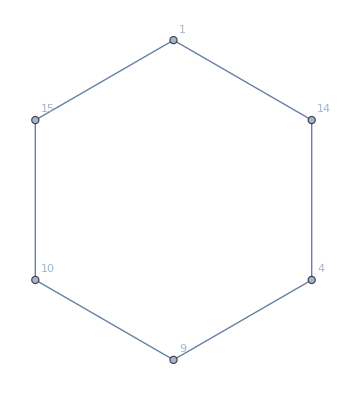

```mathematica
int=Graph[{15<->10,10<->9,9<->4,4<->14,14<->1,1<->15},VertexLabels->"Name", GraphLayout->"CircularEmbedding"]
```

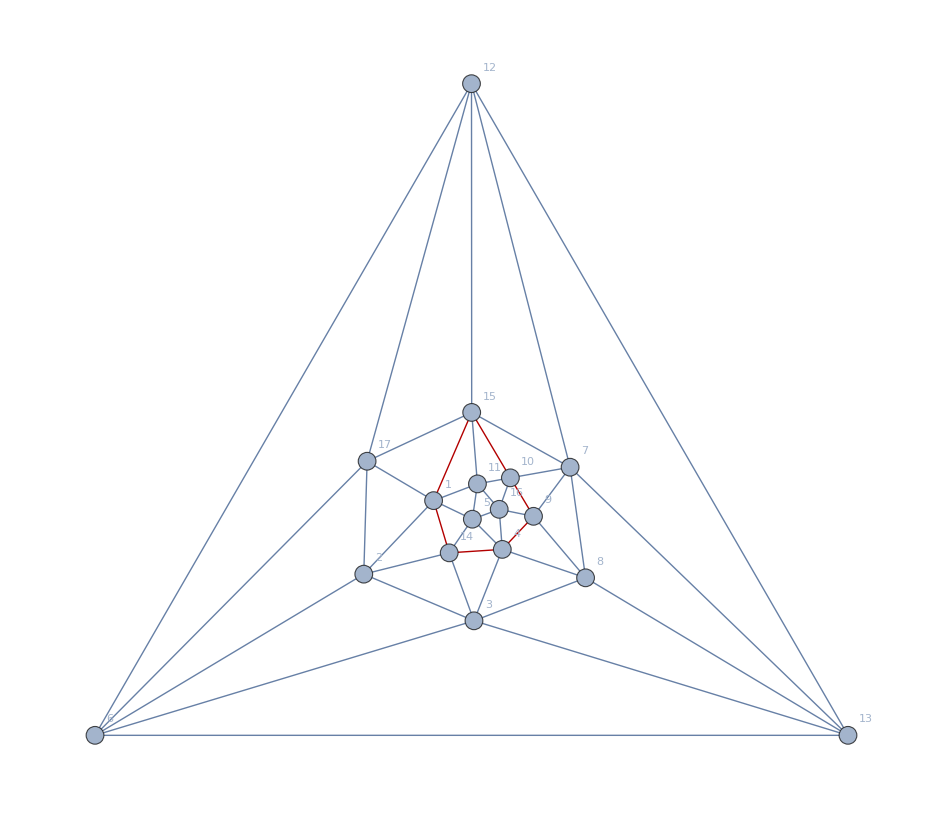

```mathematica
Graph[plantri8,GraphHighlight->EdgeList[int],GraphHighlightStyle->"Thick"]
```

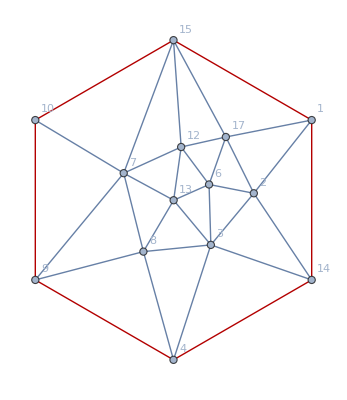

```mathematica
left=Graph[VertexDelete[plantri8,{11,16,5}],GraphHighlight->EdgeList[int],GraphHighlightStyle->"Thick"]
```

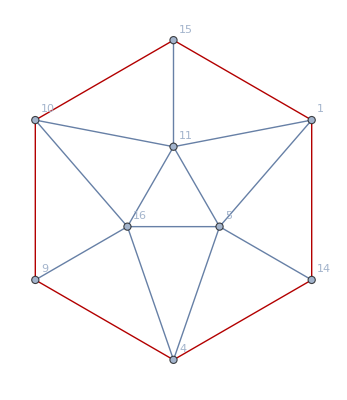

```mathematica
right=Graph[VertexDelete[plantri8,SetDifference[VertexList[left],VertexList[int]]],GraphHighlight->EdgeList[int],GraphHighlightStyle->"Thick"]
```

```mathematica
IsomorphicGraphQ[GraphUnion[left,right,GraphLayout->"TutteEmbedding",VertexLabels->"Name"],plantri8]
```

True

```mathematica
IsomorphicGraphQ[GraphUnion[left,int,GraphLayout->"TutteEmbedding",VertexLabels->"Name"],left]
```

True

```mathematica
IsomorphicGraphQ[GraphUnion[right,int,GraphLayout->"TutteEmbedding",VertexLabels->"Name"],right]
```

True

```mathematica
crall=ChromaticPolynomial[plantri8,x]//Factor
```

(-3+x) (-2+x) (-1+x) x (-11877662+36882093 x-54248780 x^2+50261369 x^3-32818907 x^4+15966933 x^5-5952318 x^6+1718826 x^7-383596 x^8+65179 x^9-8175 x^10+715 x^11-39 x^12+x^13)

```mathematica
crl=ChromaticPolynomial[left,x]//Factor
```

(-3+x) (-2+x) (-1+x) x (80126-218391 x+278994 x^2-220506 x^3+119349 x^4-46100 x^5+12819 x^6-2523 x^7+335 x^8-27 x^9+x^10)

```mathematica
crr=ChromaticPolynomial[right,x]//Factor
```

(-3+x) (-2+x) (-1+x) x (-134+222 x-158 x^2+60 x^3-12 x^4+x^5)

```mathematica
crint=ChromaticPolynomial[int,x]//Factor
```

(-1+x) x (5-10 x+10 x^2-5 x^3+x^4)

```mathematica
Factor[(crl*crr)]
```

(-3+x)^2 (-2+x)^2 (-1+x)^2 x^2 (-134+222 x-158 x^2+60 x^3-12 x^4+x^5) (80126-218391 x+278994 x^2-220506 x^3+119349 x^4-46100 x^5+12819 x^6-2523 x^7+335 x^8-27 x^9+x^10)

```mathematica
(((crl*crr))/crint)//Factor
```

((-3+x)^2 (-2+x)^2 (-1+x) x (-134+222 x-158 x^2+60 x^3-12 x^4+x^5) (80126-218391 x+278994 x^2-220506 x^3+119349 x^4-46100 x^5+12819 x^6-2523 x^7+335 x^8-27 x^9+x^10))/(5-10 x+10 x^2-5 x^3+x^4)